Machine Learning

So far in this book, when we’ve wanted the Wolfram Language to do something, we’ve written code to tell it exactly what to do. But the Wolfram Language is also set up to be able to learn what to do just by looking at examples, using the idea of machine learning.

We’ll talk about how to train the language yourself. But first let’s look at some built-in functions that have already been trained on huge numbers of examples. The Wolfram Language’s machine learning functions are improved with each new version release, so your results may be slightly different than those shown here.

LanguageIdentify takes pieces of text, and identifies what human language they’re in.

Identify the language each phrase is in:

```mathematica
LanguageIdentify[{ "thank you","merci","dar las gracias","感謝","благодарить"}]
```

{English,French,Spanish,Chinese,Russian}

The Wolfram Language can also do the considerably more difficult “artificial intelligence” task of identifying what an image is of.

Identify what an image is of:

```mathematica
ImageIdentify[-Graphics-]
```

cheetah

There’s a general function Classify, which has been taught various kinds of classification. One example is classifying the “sentiment” of text.

Upbeat text is classified as having positive sentiment:

```mathematica
Classify["Sentiment","I'm so excited to be programming"]
```

Positive

Downbeat text is classified as having negative sentiment:

```mathematica
Classify["Sentiment","math can be really hard"]
```

Negative

You can also train Classify yourself. Here’s a simple example of classifying handwritten digits as 0 or 1. You give Classify a collection of training examples, followed by a particular handwritten digit. Then it’ll tell you whether the digit you give is a 0 or 1.

With training examples, Classify correctly identifies a handwritten 0:

```mathematica
Classify[{-Graphics-->0,-Graphics-->1,-Graphics-->0,-Graphics-->1,-Graphics-->1,-Graphics-->0,-Graphics-->0,-Graphics-->1,-Graphics-->1,-Graphics-->0,-Graphics-->0,-Graphics-->0,-Graphics-->1,-Graphics-->0,-Graphics-->1,-Graphics-->0,-Graphics-->1,-Graphics-->1,-Graphics-->1},
-Graphics-]
```

0

To get some sense of how this works—and because it’s useful in its own right—let’s talk about the function Nearest, that finds what element in a list is nearest to what you supply.

Find what number in the list is nearest to 22:

```mathematica
Nearest[{10,20,30,40,50,60,70,80},22]
```

{20}

Find the nearest three numbers:

```mathematica
Nearest[{10,20,30,40,50,60,70,80},22,3]
```

{20,30,10}

Nearest can find nearest colors as well.

Find the 3 colors in the list that are nearest to the color you give:

```mathematica
Nearest[{Hue[0.],Hue[0.05],Hue[0.1],Hue[0.15000000000000002],Hue[0.2],Hue[0.25],Hue[0.30000000000000004],Hue[0.35000000000000003],Hue[0.4],Hue[0.45],Hue[0.5],Hue[0.55],Hue[0.6000000000000001],Hue[0.65],Hue[0.7000000000000001],Hue[0.75],Hue[0.8]},RGBColor[0.8727094319714808, 0.9066617343162084, 0.09569669807641734],3]
```

{Hue[0.15000000000000002],Hue[0.2],Hue[0.25]}

It also works on words.

Find the 10 words nearest to “good” in the list of words:

```mathematica
Nearest[WordList[ ],"good",10]
```

{good,food,goad,god,gold,goo,goody,goof,goon,goop}

There’s a notion of nearness for images too. And though it’s far from the whole story, this is effectively part of what ImageIdentify is using.

Something that’s again related is recognizing text (optical character recognition or OCR). Let’s make a piece of text that’s blurred.

Create an image of the word “hello”, then blur it:

```mathematica
Blur[Rasterize[Style["hello",30]],3]
```

-Graphics-

TextRecognize can still recognize the original text string in this.

Recognize text in the image:

```mathematica
TextRecognize[-Graphics-]
```

hello

If the text gets too blurred TextRecognize can’t tell what it says—and you probably can’t either.

Generate a sequence of progressively more blurred pieces of text:

```mathematica
Table[Blur[Rasterize["hello"],r],{r,0,10}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

As the text gets more blurred, TextRecognize makes a mistake, then gives up altogether:

```mathematica
Table[TextRecognize[Blur[Rasterize["hello"],r]],{r,0,10}]
```

{hello,hello,hello,hello,hello,hello,nelle,nelle,ne | le,,}

Something similar happens if we progressively blur the picture of a cheetah. When the picture is still fairly sharp, ImageIdentify will correctly identify it as a cheetah. But when it gets too blurred ImageIdentify starts thinking it’s more likely to be a wildcat, and eventually the best guess is that it’s a whortleberry.

Progressively blur a picture of a cheetah:

```mathematica
Table[Blur[-Graphics-,r],{r,0,22,2}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

When the picture gets too blurred, ImageIdentify no longer thinks it’s a cheetah:

```mathematica
Table[ImageIdentify[Blur[-Graphics-,r]],{r,0,22,2}]
```

{cheetah,cheetah,cheetah,cheetah,wildcat,Canada lynx,feline,nutria,musteline mammal,northern river otter,whortleberry,whortleberry}

ImageIdentify normally just gives what it thinks is the most likely identification. You can tell it, though, to give a list of possible identifications, starting from the most likely. Here are the top 10 possible identifications, in all categories.

ImageIdentify thinks this might be a cheetah, but it’s more likely to be a wildcat, or it could be a baboon:

```mathematica
ImageIdentify[-Graphics-,All,10]
```

{wildcat,liger,lynx,Canada lynx,jaguar,mountain lion,cheetah,patas monkey,baboon,chacma baboon}

When the image is sufficiently blurred, ImageIdentify can have wild ideas about what it might be:

```mathematica
ImageIdentify[-Graphics-,All,10]
```

{whortleberry,blueberry,Alaskan malamute,berry,northern fur seal,guadalupe fur seal,California sea lion,Australian sea lion,Steller sea lion,sled dog}

In machine learning, one often gives training that explicitly says, for example, “this is a cheetah”, “this is a lion”. But one also often just wants to automatically pick out categories of things without any specific training.

One way to start doing this is to take a collection of things—say colors—and then to find clusters of similar ones. This can be achieved using FindClusters.

Collect “clusters” of similar colors into separate lists:

```mathematica
FindClusters[{RGBColor[{0.048175746346922704, 0.8856231902848692, 0.002187262571789972}],RGBColor[{0.9543437880041175, 0.9364915417894851, 0.08314980598714755}],RGBColor[{0.8527294202095301, 0.15459949958575997, 0.08139444813034824}],RGBColor[{0.12965437429396431, 0.8338364200576898, 0.16859742903104202}],RGBColor[{0.14189318640501342, 0.8685451286121387, 0.10426943556314977}],RGBColor[{0.9244703510275273, 0.001783470411052479, 0.14318146272477922}],RGBColor[{0.8340523614444824, 0.038129646837010533, 0.09354464468116397}],RGBColor[{0.06423181065333894, 0.9361486399945784, 0.08411970647251821}],RGBColor[{0.8676164929883508, 0.8866580065099905, 0.024086278089002183}],RGBColor[{0.8577958146408966, 0.8374035340744639, 0.0071190816223388464}],RGBColor[{0.9967431643372854, 0.969475575859666, 0.12251095291379577}],RGBColor[{0.8543889209256321, 0.09697598692920356, 0.10750903324099509}],RGBColor[{0.8500363984900003, 0.9263311671408848, 0.13924242858059316}],RGBColor[{0.9879209034166253, 0.8377732017482453, 0.15613661869756118}],RGBColor[{0.9573167308698426, 0.1507116093826361, 0.09832234398916928}],RGBColor[{0.04278634258158939, 0.9055378427790535, 0.0003309996431954121}],RGBColor[{0.8058039405531526, 0.8318774133774354, 0.10151558699591279}],RGBColor[{0.006814389873512461, 0.9336694049188562, 0.06907220235176909}],RGBColor[{0.9450158125329948, 0.9670907305400336, 0.05040029871534907}],RGBColor[{0.9752641706478989, 0.8013981246170678, 0.10899973580393796}],RGBColor[{0.16590548598015492, 0.9015045495499641, 0.09828783196817376}],RGBColor[{0.10048980936842117, 0.9171495192304465, 0.16131399976146749}]}]
```

{{RGBColor[{0.048175746346922704, 0.8856231902848692, 0.002187262571789972}],RGBColor[{0.12965437429396431, 0.8338364200576898, 0.16859742903104202}],RGBColor[{0.14189318640501342, 0.8685451286121387, 0.10426943556314977}],RGBColor[{0.06423181065333894, 0.9361486399945784, 0.08411970647251821}],RGBColor[{0.04278634258158939, 0.9055378427790535, 0.0003309996431954121}],RGBColor[{0.006814389873512461, 0.9336694049188562, 0.06907220235176909}],RGBColor[{0.16590548598015492, 0.9015045495499641, 0.09828783196817376}],RGBColor[{0.10048980936842117, 0.9171495192304465, 0.16131399976146749}]},{RGBColor[{0.9543437880041175, 0.9364915417894851, 0.08314980598714755}],RGBColor[{0.8676164929883508, 0.8866580065099905, 0.024086278089002183}],RGBColor[{0.8577958146408966, 0.8374035340744639, 0.0071190816223388464}],RGBColor[{0.9967431643372854, 0.969475575859666, 0.12251095291379577}],RGBColor[{0.8500363984900003, 0.9263311671408848, 0.13924242858059316}],RGBColor[{0.9879209034166253, 0.8377732017482453, 0.15613661869756118}],RGBColor[{0.8058039405531526, 0.8318774133774354, 0.10151558699591279}],RGBColor[{0.9450158125329948, 0.9670907305400336, 0.05040029871534907}],RGBColor[{0.9752641706478989, 0.8013981246170678, 0.10899973580393796}]},{RGBColor[{0.8527294202095301, 0.15459949958575997, 0.08139444813034824}],RGBColor[{0.9244703510275273, 0.001783470411052479, 0.14318146272477922}],RGBColor[{0.8340523614444824, 0.038129646837010533, 0.09354464468116397}],RGBColor[{0.8543889209256321, 0.09697598692920356, 0.10750903324099509}],RGBColor[{0.9573167308698426, 0.1507116093826361, 0.09832234398916928}]}}

You can get a different view by connecting each color to the three most similar colors in the list, then making a graph out of the connections. In the particular example here, there end up being three disconnected subgraphs.

Create a graph of connections based on nearness in “color space”:

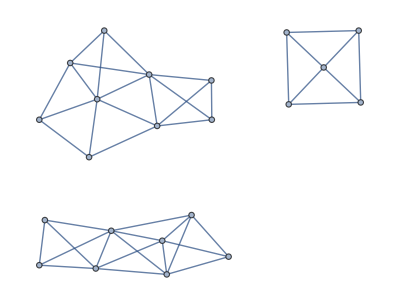

```mathematica
NearestNeighborGraph[{RGBColor[{0.048175746346922704, 0.8856231902848692, 0.002187262571789972}],RGBColor[{0.9543437880041175, 0.9364915417894851, 0.08314980598714755}],RGBColor[{0.8527294202095301, 0.15459949958575997, 0.08139444813034824}],RGBColor[{0.12965437429396431, 0.8338364200576898, 0.16859742903104202}],RGBColor[{0.14189318640501342, 0.8685451286121387, 0.10426943556314977}],RGBColor[{0.9244703510275273, 0.001783470411052479, 0.14318146272477922}],RGBColor[{0.8340523614444824, 0.038129646837010533, 0.09354464468116397}],RGBColor[{0.06423181065333894, 0.9361486399945784, 0.08411970647251821}],RGBColor[{0.8676164929883508, 0.8866580065099905, 0.024086278089002183}],RGBColor[{0.8577958146408966, 0.8374035340744639, 0.0071190816223388464}],RGBColor[{0.9967431643372854, 0.969475575859666, 0.12251095291379577}],RGBColor[{0.8543889209256321, 0.09697598692920356, 0.10750903324099509}],RGBColor[{0.8500363984900003, 0.9263311671408848, 0.13924242858059316}],RGBColor[{0.9879209034166253, 0.8377732017482453, 0.15613661869756118}],RGBColor[{0.9573167308698426, 0.1507116093826361, 0.09832234398916928}],RGBColor[{0.04278634258158939, 0.9055378427790535, 0.0003309996431954121}],RGBColor[{0.8058039405531526, 0.8318774133774354, 0.10151558699591279}],RGBColor[{0.006814389873512461, 0.9336694049188562, 0.06907220235176909}],RGBColor[{0.9450158125329948, 0.9670907305400336, 0.05040029871534907}],RGBColor[{0.9752641706478989, 0.8013981246170678, 0.10899973580393796}],RGBColor[{0.16590548598015492, 0.9015045495499641, 0.09828783196817376}],RGBColor[{0.10048980936842117, 0.9171495192304465, 0.16131399976146749}]},3,VertexLabels->All]
```

A dendrogram is a tree-like plot that lets you see a whole hierarchy of what’s near what.

Show nearby colors successively grouped together:

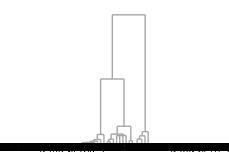

```mathematica
Dendrogram[{RGBColor[{0.048175746346922704, 0.8856231902848692, 0.002187262571789972}],RGBColor[{0.9543437880041175, 0.9364915417894851, 0.08314980598714755}],RGBColor[{0.8527294202095301, 0.15459949958575997, 0.08139444813034824}],RGBColor[{0.12965437429396431, 0.8338364200576898, 0.16859742903104202}],RGBColor[{0.14189318640501342, 0.8685451286121387, 0.10426943556314977}],RGBColor[{0.9244703510275273, 0.001783470411052479, 0.14318146272477922}],RGBColor[{0.8340523614444824, 0.038129646837010533, 0.09354464468116397}],RGBColor[{0.06423181065333894, 0.9361486399945784, 0.08411970647251821}],RGBColor[{0.8676164929883508, 0.8866580065099905, 0.024086278089002183}],RGBColor[{0.8577958146408966, 0.8374035340744639, 0.0071190816223388464}],RGBColor[{0.9967431643372854, 0.969475575859666, 0.12251095291379577}],RGBColor[{0.8543889209256321, 0.09697598692920356, 0.10750903324099509}],RGBColor[{0.8500363984900003, 0.9263311671408848, 0.13924242858059316}],RGBColor[{0.9879209034166253, 0.8377732017482453, 0.15613661869756118}],RGBColor[{0.9573167308698426, 0.1507116093826361, 0.09832234398916928}],RGBColor[{0.04278634258158939, 0.9055378427790535, 0.0003309996431954121}],RGBColor[{0.8058039405531526, 0.8318774133774354, 0.10151558699591279}],RGBColor[{0.006814389873512461, 0.9336694049188562, 0.06907220235176909}],RGBColor[{0.9450158125329948, 0.9670907305400336, 0.05040029871534907}],RGBColor[{0.9752641706478989, 0.8013981246170678, 0.10899973580393796}],RGBColor[{0.16590548598015492, 0.9015045495499641, 0.09828783196817376}],RGBColor[{0.10048980936842117, 0.9171495192304465, 0.16131399976146749}]}]
```

When we compare things—whether they’re colors or pictures of animals—we can think of identifying certain features that allow us to distinguish them. For colors, a feature might be how light the color is, or how much red it contains. For pictures of animals, a feature might be how furry the animal looks, or how pointy its ears are.

In the Wolfram Language, FeatureSpacePlot takes collections of objects and tries to find what it considers the “best” distinguishing features of them, then uses the values of these to position objects in a plot.

FeatureSpacePlot doesn’t explicitly say what features it’s using—and actually they’re usually quite hard to describe. But what happens in the end is that FeatureSpacePlot arranges things so that objects that have similar features are drawn nearby.

FeatureSpacePlot makes similar colors be placed nearby:

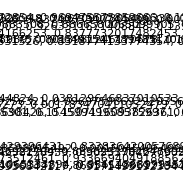

```mathematica
FeatureSpacePlot[{RGBColor[{0.048175746346922704, 0.8856231902848692, 0.002187262571789972}],RGBColor[{0.9543437880041175, 0.9364915417894851, 0.08314980598714755}],RGBColor[{0.8527294202095301, 0.15459949958575997, 0.08139444813034824}],RGBColor[{0.12965437429396431, 0.8338364200576898, 0.16859742903104202}],RGBColor[{0.14189318640501342, 0.8685451286121387, 0.10426943556314977}],RGBColor[{0.9244703510275273, 0.001783470411052479, 0.14318146272477922}],RGBColor[{0.8340523614444824, 0.038129646837010533, 0.09354464468116397}],RGBColor[{0.06423181065333894, 0.9361486399945784, 0.08411970647251821}],RGBColor[{0.8676164929883508, 0.8866580065099905, 0.024086278089002183}],RGBColor[{0.8577958146408966, 0.8374035340744639, 0.0071190816223388464}],RGBColor[{0.9967431643372854, 0.969475575859666, 0.12251095291379577}],RGBColor[{0.8543889209256321, 0.09697598692920356, 0.10750903324099509}],RGBColor[{0.8500363984900003, 0.9263311671408848, 0.13924242858059316}],RGBColor[{0.9879209034166253, 0.8377732017482453, 0.15613661869756118}],RGBColor[{0.9573167308698426, 0.1507116093826361, 0.09832234398916928}],RGBColor[{0.04278634258158939, 0.9055378427790535, 0.0003309996431954121}],RGBColor[{0.8058039405531526, 0.8318774133774354, 0.10151558699591279}],RGBColor[{0.006814389873512461, 0.9336694049188562, 0.06907220235176909}],RGBColor[{0.9450158125329948, 0.9670907305400336, 0.05040029871534907}],RGBColor[{0.9752641706478989, 0.8013981246170678, 0.10899973580393796}],RGBColor[{0.16590548598015492, 0.9015045495499641, 0.09828783196817376}],RGBColor[{0.10048980936842117, 0.9171495192304465, 0.16131399976146749}]}]
```

If one uses, say, 100 colors picked completely at random, then FeatureSpacePlot will again place colors it considers similar nearby.

100 random colors laid out by FeatureSpacePlot:

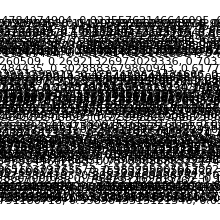

```mathematica
FeatureSpacePlot[RandomColor[100]]
```

Let’s try the same kind of thing with images of letters.

Make a rasterized image of each letter in the alphabet:

```mathematica
Table[Rasterize[FromLetterNumber[n]],{n,26}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

FeatureSpacePlot will use visual features of these images to lay them out. The result is that letters that look similar—like y and v or e and c—will wind up nearby.

```mathematica
FeatureSpacePlot[Table[Rasterize[FromLetterNumber[n]],{n,26}]]
```

-Graphics-

Here’s the same thing, but now with pictures of cats, cars and chairs. FeatureSpacePlot immediately separates the different kinds of things.

FeatureSpacePlot places photographs of different kinds of things quite far apart:

```mathematica
FeatureSpacePlot[{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}]
```

-Graphics-

Vocabulary

LanguageIdentify[text] |   | identify what human language text is in 
ImageIdentify[image] |   | identify what an image is of 
TextRecognize[text] |   | recognize text from an image (OCR) 
Classify[training,data] |   | classify data on the basis of training examples 
Nearest[list,item] |   | find what element of list is nearest to item 
FindClusters[list] |   | find clusters of similar items 
NearestNeighborGraph[list,n] |   | connect elements of list to their n nearest neighbors 
Dendrogram[list] |   | make a hierarchical tree of relations between items
FeatureSpacePlot[list] |   | plot elements of list in an inferred “feature space”

"16 Exercises Available"
"with 7 extras" | "Get Started »"

Identify what language the word “ajatella” comes from. »

| Expected output: |  
  | "Finnish" |

Apply ImageIdentify to an image of a tiger, getting the image using ctrl=. »

| Expected output: |  
  | "tiger" |

Make a table of image identifications for an image of a tiger, blurred by an amount from 1 to 5. »

| Expected output: |  
  | {"tiger","tiger","tiger","spiny-finned fish","fish"} |

Classify the sentiment of “I’m so happy to be here”. »

| Expected output: |  
  | "Positive" |

Find the 10 words in WordList[ ] that are nearest to “happy”. »

| Expected output: |  
  | {"happy","haply","harpy","nappy","sappy","apply","campy","choppy","guppy","hairy"} |

Generate 20 random numbers up to 1000 and find which 3 are nearest to 100. »

| Sample expected output: |  
  | {94,91,133} |

Generate a list of 10 random colors, and find which 5 are closest to Red. »

| Sample expected output: |  
  | {RGBColor[0.9132382296127133, 0.1052875704634939, 0.1081561232856334],RGBColor[0.9771026336083766, 0.363796063619348, 0.01077019070224905],RGBColor[0.9549993293169798, 0.21676827484502326, 0.2513102591499172],RGBColor[0.8483679553563124, 0.30385712208149696, 0.15484335046598763],RGBColor[0.9594790623807896, 0.5046051552943853, 0.18946774256928367]} |

Of the first 100 squares, find the one nearest to 2000. »

| Expected output: |  
  | 2025 |

Find the 3 European flags nearest to the flag of Brazil. »

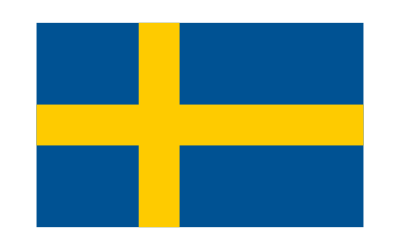
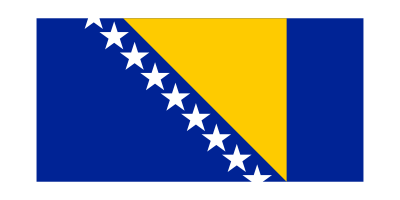
| Expected output: |  
  | {-Graphics-,-Graphics-,-Graphics-} |

Make a graph of the 2 nearest neighbors of each color in Table[Hue[h],{h,0,1,.05}]. »

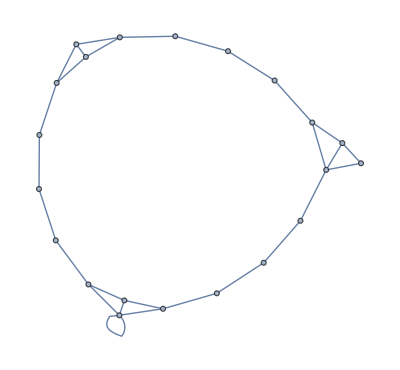
| Expected output: |  
  | -Graphics- |

Generate a list of 100 random numbers from 0 to 100, and make a graph of the 2 nearest neighbors of each one. »

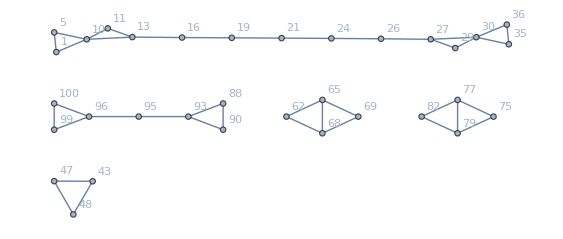
| Sample expected output: |  
  | -Graphics- |

Collect the flags of Asia into clusters of similar flags. »

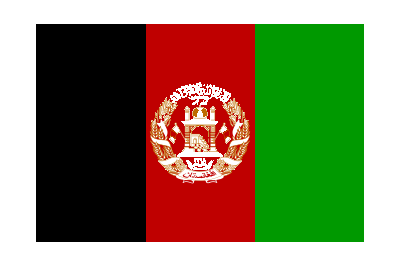
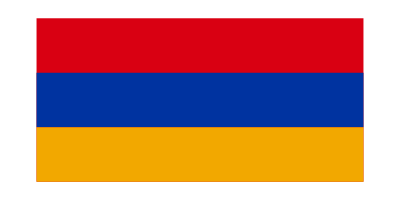
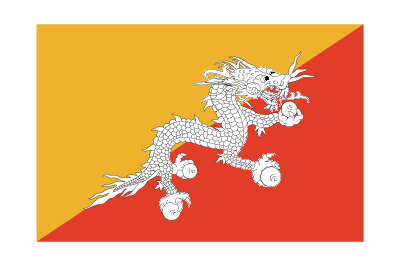

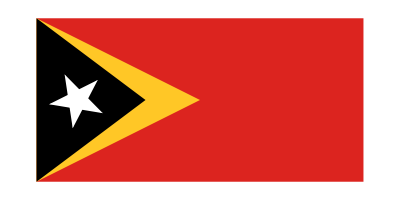
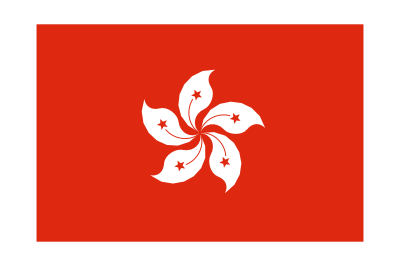
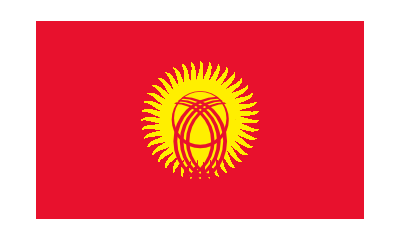
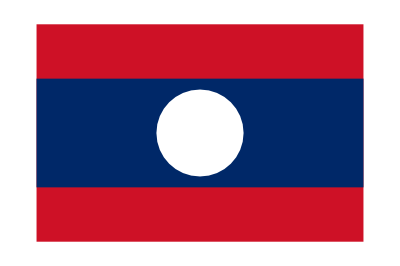
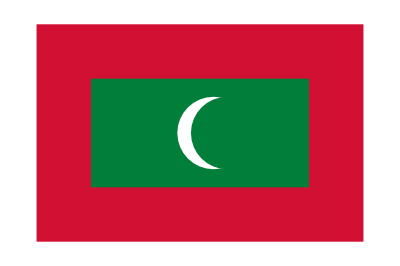

| Expected output: |  
  | {{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-},{-Graphics-,-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-}} |

Make raster images of the letters of the alphabet at size 20, then make a graph of the 2 nearest neighbors of each one. »

| Expected output: |  
  | -Graphics- |

Generate a table of the results from applying TextRecognize to the EdgeDetect of the word “programming” rasterized at sizes between 10 and 20. »

| Expected output: |  
  | {"Bigceieelmmn aye","moana","PLM eel NE","reo Ae M Nae:","programm ng","programming","mortal mney","programming","programm ng","moral nna","imeyca eect"} |

Make a dendrogram for images of the first 10 letters of the alphabet. »

| Expected output: |  
  | -Graphics- |

Make a feature space plot for the uppercase letters of the alphabet. »

| Expected output: |  
  | -Graphics- |

Make a table of image identifications for a picture of the Eiffel Tower, blurred by an amount from 1 to 5. »

| Expected output: |  
  | {"Eiffel Tower","Eiffel Tower","tower","stupa","stupa"} |

Classify the sentiment of the Wikipedia article on “happiness”. »

| Expected output: |  
  | "Neutral" |

Of colors in the list Table[Hue[h],{h,0,1,.05}], find which are the 3 nearest to Pink. »

| Expected output: |  
  | {Hue[0.9500000000000001],Hue[0.9],Hue[0.05]} |

Compute all fractions i/j for i and j up to 500, and find the 10 fractions closest to pi. »

| Expected output: |  
  | {355/113,377/120,333/106,399/127,311/99,421/134,443/141,289/92,465/148,487/155} |

Generate a list of 10 random numbers from 0 to 10, and make a graph of the 3 nearest neighbors of each one. »

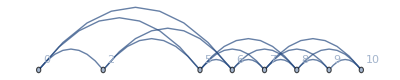
| Expected output: |  
  | -Graphics- |

Find clusters of similar colors in a list of 100 random colors. »

| Expected output: |  
  | {{RGBColor[0.8116438051434329, 0.8547919864863347, 0.7807710853793401],RGBColor[0.2983278570382957, 0.9907444932950316, 0.9284043344039434],RGBColor[0.18676117011450066, 0.5486089602170863, 0.04303247680226141],RGBColor[0.4044608902823441, 0.9788998961090443, 0.8108975624714536],RGBColor[0.5308001574813235, 0.9503472359039511, 0.8646083755834806],RGBColor[0.5926608241659339, 0.4671421812435703, 0.027570072930602985],RGBColor[0.49843743964638865, 0.7588128836239783, 0.6588996785867525],RGBColor[0.6788691428209239, 0.8865118691450595, 0.06859340947663295],RGBColor[0.3966954095359472, 0.9303983446364068, 0.27133513969525125],RGBColor[0.7496777159050012, 0.8414031368083361, 0.29000881481349006],RGBColor[0.1722869702422274, 0.42066881136044554, 0.18877704427888808],RGBColor[0.020568097401979735, 0.32843933224376776, 0.2578912775452169],RGBColor[0.4276762158276948, 0.9445301871184215, 0.6339408432442302],RGBColor[0.3449333805776824, 0.8214093187031501, 0.00535396147946221],RGBColor[0.9595114792486563, 0.9614567195621035, 0.09956803288245264],RGBColor[0.13927723404143122, 0.9837658758454813, 0.6275322853052734],RGBColor[0.4129872979782936, 0.599123151026224, 0.5563798982651478],RGBColor[0.5517409716001453, 0.7226268672047083, 0.04296745155978088],RGBColor[0.2471012449687613, 0.6622219052252245, 0.34136700529740893],RGBColor[0.00852878273374924, 0.7623891609381206, 0.495048201930645],RGBColor[0.410530117230961, 0.65951899493187, 0.31274019237510875],RGBColor[0.14914425266109754, 0.8632288046219025, 0.2165769996518021],RGBColor[0.5019554020533212, 0.5771425709059108, 0.4324648041012522],RGBColor[0.2375846642639532, 0.7953276430316651, 0.9346352336682711],RGBColor[0.5670638896981823, 0.30694748662903737, 0.07724772234151844],RGBColor[0.9836330486106633, 0.9337141420685637, 0.45110780147188234],RGBColor[0.548151102001315, 0.9273818734933321, 0.6138604019189067],RGBColor[0.08996343949980967, 0.7502285322367264, 0.7647837622874905],RGBColor[0.9554445238224603, 0.9118174885785313, 0.7586039763217882],RGBColor[0.12407876246761118, 0.8951986963374581, 0.405054951518828],RGBColor[0.3518853673765441, 0.6267881822227646, 0.01601455063963053],RGBColor[0.38175543134617906, 0.6109792496345561, 0.30321055377645356],RGBColor[0.5015968883258048, 0.9477341972992892, 0.7518749706067847],RGBColor[0.4853791041906068, 0.9983056811536988, 0.059586297674913524],RGBColor[0.39598681356054666, 0.5894657294683947, 0.2897133293523855],RGBColor[0.06510008212093177, 0.7580810151353965, 0.4838966525370989],RGBColor[0.02229677965825383, 0.35028891391213257, 0.0684550207396537],RGBColor[0.15578960479774717, 0.33156505911261824, 0.10795082362400787],RGBColor[0.9666406011133539, 0.6653552686335491, 0.5546554666254075],RGBColor[0.21832422216206182, 0.4452088456726624, 0.34195667187604584],RGBColor[0.4939446101923697, 0.31678858836269796, 0.11346988660388835],RGBColor[0.9566388456878347, 0.9651195544633302, 0.9076564789046491],RGBColor[0.4000855073593619, 0.39588066174906866, 0.1685452332949151],RGBColor[0.5700736595139675, 0.4069545472059297, 0.1981313907220874],RGBColor[0.16637070232988593, 0.6273450506223697, 0.6129198387249786],RGBColor[0.15217789308335927, 0.6805446503579162, 0.7536712821543405],RGBColor[0.011500166973726689, 0.9344737120630893, 0.41519231703372195],RGBColor[0.6487763190386047, 0.9218976224198998, 0.711816672844579],RGBColor[0.47327935747334204, 0.8834140175937308, 0.33245673464773584],RGBColor[0.25560515056407795, 0.8012401319897553, 0.15094027368448049],RGBColor[0.13360546814982577, 0.7871863239201633, 0.018599162734135977],RGBColor[0.38337417819768205, 0.4988952587556723, 0.08321860516969015],RGBColor[0.4181367040733106, 0.49313383402211364, 0.10167945128775124],RGBColor[0.4812053533680498, 0.873332380181423, 0.327028956990717],RGBColor[0.5269434582467774, 0.8294337802982428, 0.1734709900484559]},{RGBColor[0.37266534273681007, 0.38750269832660855, 0.3948182017762212],RGBColor[0.733606571264461, 0.4291909747287308, 0.4301886698173236],RGBColor[0.17707863410973768, 0.672607405954065, 0.8338273497920801],RGBColor[0.8745580077995285, 0.08910005366925322, 0.5820198361552016],RGBColor[0.9090294322469556, 0.2839329014344203, 0.5231271919589293],RGBColor[0.4864384781423896, 0.2590016473319656, 0.8939198034327294],RGBColor[0.2674220618976657, 0.5345197867819858, 0.7888815584252213],RGBColor[0.18736123677107708, 0.3952086052502788, 0.86460527303447],RGBColor[0.7776461280660796, 0.8643601244579295, 0.9944319426310919],RGBColor[0.10244743490058794, 0.1869170597224914, 0.6271170684614624],RGBColor[0.4573447796522936, 0.007181376876192136, 0.566195028583903],RGBColor[0.23258722219837846, 0.08344742427005825, 0.30644177688225716],RGBColor[0.711485166849398, 0.017375777675906035, 0.7454946682315056],RGBColor[0.31452599923983104, 0.6908103742720597, 0.9463506847311731],RGBColor[0.922559309792595, 0.2703946335791436, 0.09665543181913394],RGBColor[0.11122524183982829, 0.12772449779541217, 0.6139200516853858],RGBColor[0.6357194627252103, 0.15357943517679362, 0.860476954867391],RGBColor[0.4431832834876257, 0.18321465791748515, 0.7764518003586576],RGBColor[0.3553518860908462, 0.6443320866741731, 0.7499636864238166],RGBColor[0.8943854155561495, 0.03560200287351467, 0.16578917868909593],RGBColor[0.6672396717157738, 0.3586192991395154, 0.8976595916455246],RGBColor[0.37001635641206, 0.3047563933568622, 0.7684408201506054],RGBColor[0.38698691150966935, 0.10328204902950966, 0.8013210231747274],RGBColor[0.29215345853340424, 0.35497646703617836, 0.6346432521789236],RGBColor[0.9678407581110904, 0.025426491397912976, 0.587777889276665],RGBColor[0.4918965330955356, 0.29233426982370303, 0.5281824844462943],RGBColor[0.1252423737911874, 0.5183189386335805, 0.7491160058315705],RGBColor[0.9765556387211944, 0.12357617097291551, 0.5068373458296718],RGBColor[0.8227934753153485, 0.3797246867796864, 0.6782582898466567],RGBColor[0.6820734720667967, 0.43856527685111324, 0.8695673460178908],RGBColor[0.11654903299881392, 0.07006336344132391, 0.56484752468554],RGBColor[0.6402988781363921, 0.035330434441392944, 0.28001275709114415],RGBColor[0.4249737173056105, 0.08087713350797054, 0.5561568741925262],RGBColor[0.7495302686726302, 0.3453338459340154, 0.3119406215616949],RGBColor[0.836090631447431, 0.10393312541533217, 0.9133348768403533],RGBColor[0.19151655035273674, 0.14390156161230028, 0.5247101500257152],RGBColor[0.8789399682999111, 0.042929493135203334, 0.19233219566452364],RGBColor[0.8279081820793655, 0.007601665021679249, 0.007776314948584773],RGBColor[0.8905220469868362, 0.6720465313460078, 0.8782899541874138],RGBColor[0.4739838883353795, 0.01643240988333261, 0.7672816104627056],RGBColor[0.73262590528079, 0.4345872718612065, 0.9513218213654053],RGBColor[0.7193138046226939, 0.736637476380962, 0.9909551197977506],RGBColor[0.5532261835871646, 0.1424067735626049, 0.6840947116434117],RGBColor[0.24015696649735507, 0.2276921291555416, 0.5618669828113934],RGBColor[0.3614530023699991, 0.23838000474075272, 0.351099450461986]}} |

Make a feature space plot for both upper and lowercase letters of the alphabet. »

| Expected output: |  
  | -Graphics- |

Q&A

How come I’m getting different results from the ones shown here?

Probably because Wolfram Language machine learning functions are continually getting more training—and so their results may change, hopefully always getting better. For TextRecognize, the results can depend in detail on the fonts used, and exactly how they’re rendered and rasterized on your computer.

How does ImageIdentify work inside?

It’s based on artificial neural networks inspired by the way brains seem to work. It’s been trained with millions of example images, from which it’s progressively learned to make distinctions. And a bit like in the game of “twenty questions”, by using enough of these distinctions it can eventually determine what an image is of.

How many kinds of things can ImageIdentify recognize?

At least 10,000—which is more than a typical human. (There are about 5000 “picturable nouns” in English.)

What makes ImageIdentify give a wrong answer?

A common cause is that what it’s asked about isn’t close enough to anything it’s been trained on. This can happen if something is in an unusual configuration or environment (for example, if a boat is not on a bluish background). ImageIdentify usually tries to find some kind of match, and the mistakes it makes often seem very “humanlike”.

Can I ask ImageIdentify the probabilities it assigns to different identifications?

Yes. For example, to find the probabilities for the top 10 identifications in all categories use ImageIdentify[image, All, 10, "Probability"].

How many examples does Classify typically need to work well?

If the general area (like everyday images) is one it already knows well, then as few as a hundred. But in areas that are new, it can take many millions of examples to achieve good results.

How does Nearest figure out a distance between colors?

It uses the function ColorDistance, which is based on a model of human color vision.

How does Nearest determine nearby words?

By looking at those at the smallest EditDistance, that is, reached by the smallest number of single-letter insertions, deletions and substitutions.

What features does FeatureSpacePlot use?

There’s no easy answer. When it’s given a collection of things, it’ll learn features that distinguish them—though it’s typically primed by having seen many other things of the same general type (like images).

Tech Notes

The Wolfram Language stores its latest machine learning classifiers in the cloud—but if you’re using a desktop system, they’ll automatically be downloaded, and then they’ll run locally.

BarcodeImage and BarcodeRecognize work with bar codes and QR codes instead of pure text.

ImageIdentify is the core of what the imageidentify.com website does.

If you just give Classify training examples, it’ll produce a ClassifierFunction that can later be applied to many different pieces of data. This is pretty much always how Classify is used in practice.

You can get a large standard training set of handwritten digits using ResourceData["MNIST"].

Classify automatically picks between methods such as logistic regression, naive Bayes, random forests and support vector machines, as well as neural networks.

FindClusters does unsupervised machine learning, where the computer just looks at data without being told anything about it. Classify does supervised machine learning, being given a set of training examples.

Dendrogram does hierarchical clustering, and can be used to reconstruct evolutionary trees in areas like bioinformatics and historical linguistics.

FeatureSpacePlot does dimension reduction, taking data that’s represented by many parameters, and finding a good way to “project” these down so they can be plotted in 2D.

Rasterize/@Alphabet[ ] is a better way to make a list of rasterized letters, but we won’t talk about /@ until Section 25.

FeatureExtraction lets you get out the feature vectors used by FeatureSpacePlot.

FeatureNearest is like Nearest except that it learns what should be considered near by looking at the actual data you give. It’s what you need to do something like build an image-search function.

NetModel gives you immediate access to a large number of prebuilt nets from the continually updated Wolfram Neural Net Repository.

You can build and train your own neural nets in the Wolfram Language using functions like NetChain, NetGraph and NetTrain. You can include prebuilt nets from NetModel.

More to Explore

Guide to Machine Learning in the Wolfram Language »